```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/michael/Documents/CS205/team07/verification

Import and take means from the results of running the shell script:

```mathematica
importToMeans[ext_,len_]:=Block[{imports,vectors},
imports=Import/@FileNames["*.out",ext];
vectors=(#[[1;;len]]//Transpose)[[4]]&/@imports;
Mean[vectors]
]
```

The four-way parallel experiments report results on a per-thread basis, not total.  Sum over all threads:

```mathematica
fourtoone[list_]:=Table[Take[list,{(index - 1) * 4 + 1, index * 4}]//Total,{index,1,1000}] (* Thanks to an OpenMP barrier, we are guaranteed to get all output from one episode before any thread starts on the next. *)
```

```mathematica
means={importToMeans["kretchmar1",1000],(importToMeans["kretchmar4",4000]//fourtoone)/4};  (* This will take a while. *)
```

The experiments report the fraction of correct actions taken in the current episode.  Take the average for all episodes:

```mathematica
firstNAverage[l_,n_]:=Sum[l[[j]],{j,1,n}]/n
```

Finally, plot the results:

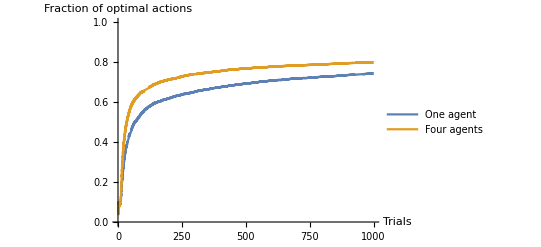

```mathematica
Plot[{firstNAverage[means[[1]],x],firstNAverage[means[[2]],x]},{x,1,1000},PlotRange->{0,1},PlotLegends->{"One agent","Four agents"},AxesLabel->{"Trials","Fraction of optimal actions"}]
```